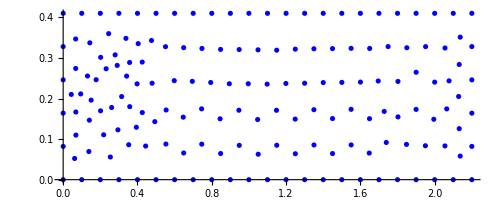

162

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/solution/snapshots/csv/vertex_mesh_n_1.csv"]
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->Automatic]
Length[tabve]
```